```mathematica
ClearAll["Global`*"];
```

```mathematica
c=3×10^8;
```

```mathematica
m=mo/(√(1-v^2/c^2));
Δx=Δxo×√(1-v^2/c^2);
Δy=Δyo;
Δz=Δzo;
```

```mathematica
V=Δx×Δy×Δz;
ρ=m/V/.mo/(Δxo×Δyo×Δzo)->ρo;
```

```mathematica
r1=Solve[ρ==ρo+x×ρo,v]
```

{{v→-(300000000 √x)/(√(1+x))},{v→(300000000 √x)/(√(1+x))}}

```mathematica
v[x_]=v/.r1[[2]];
```

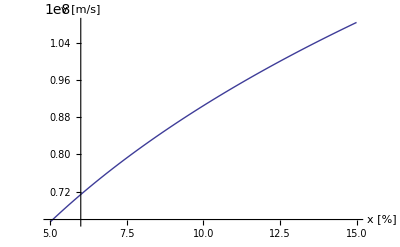

```mathematica
Plot[v[x/100],{x,5,15},
AxesLabel->{"x  [%]","v [m/s]"}]
```